```mathematica
ClearAll["Global`*"];
ClearAll[m];
```

```mathematica
ExtractData[file_]:=Module[{data,shadow,measure,lines,line,xmin,xmax,ymin,ymax,xc,yc,Dc,Dx,Dy,newLine,polarLine,r,rbar,σr,LHratio,area},
data=Import[file];
shadow=EdgeDetect[data,30];(*should test carefully before changing it*)
line=ImageValuePositions[shadow,1]-1024;
{xmin,xmax}=MinMax[line⟦All,1⟧];
{ymin,ymax}=MinMax[line⟦All,2⟧];
{xc,yc}={(xmin+xmax)/2,(ymin+ymax)/2};
Dc=Abs@xc;
{Dx,Dy}={xmax-xmin,ymax-ymin};
LHratio=Dx/Dy;
newLine=Union[line,SameTest->(Norm[#1-#2]<5&)];(*remove very close points*)
polarLine=DeleteDuplicates[{ArcTan[#⟦1⟧-xc,#⟦2⟧],√((#⟦1⟧-xc)^2+(#⟦2⟧)^2)}&/@newLine,#1⟦1⟧==#2⟦1⟧&];
polarLine=Join[Select[SortBy[polarLine,First],#⟦1⟧>0&],{#⟦1⟧+2π,#⟦2⟧}&/@Select[SortBy[polarLine,First],#⟦1⟧<0&]];
r02pi=polarLine[[1,2]];
AppendTo[polarLine,{0,r02pi}];
AppendTo[polarLine,{2π,r02pi}];
r=Interpolation[polarLine,InterpolationOrder->0];
rbar=NIntegrate[r[α]/(2π),{α,0,2π}];
σr=√NIntegrate[(r[α]-rbar)^2/(2π),{α,0,2π}];
area=NIntegrate[1/2 r[α]^2,{α,0,2π}];
{line,xmin,xmax,ymin,ymax,xc,yc,newLine,polarLine,r,Dc,Dx,Dy,LHratio,rbar,σr,area}];
```

```mathematica
FNs=FileNames[FileNameJoin[{NotebookDirectory[],"KerrQED*_bw.png"}]]
```

{D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQED-0.1_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQED-0.2_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQED-0.3_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQED-0.4_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQED-0.5_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQED-0.6_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQED-0.7_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQED-0.8_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQED-0.9_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQEDkmax-0.1_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQEDkmax-0.2_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQEDkmax-0.3_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQEDkmax-0.4_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQEDkmax-0.5_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQEDkmax-0.6_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQEDkmax-0.7_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQEDkmax-0.8_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQEDkmax-0.9_bw.png}

```mathematica
FNtab=Table[FNs[[m+9n]],{m,1,9},{n,0,1}]
```

{{D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQED-0.1_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQEDkmax-0.1_bw.png},{D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQED-0.2_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQEDkmax-0.2_bw.png},{D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQED-0.3_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQEDkmax-0.3_bw.png},{D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQED-0.4_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQEDkmax-0.4_bw.png},{D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQED-0.5_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQEDkmax-0.5_bw.png},{D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQED-0.6_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQEDkmax-0.6_bw.png},{D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQED-0.7_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQEDkmax-0.7_bw.png},{D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQED-0.8_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQEDkmax-0.8_bw.png},{D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQED-0.9_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\a=0.2\KerrQEDkmax-0.9_bw.png}}

```mathematica
shapedata=Map[ExtractData,FNtab,{2}];
shrink=Table[shapedata[[m,2,-1]]/shapedata[[m,1,-1]],{m,1,9}]
```

{0.652717,0.654613,0.658026,0.662542,0.669529,0.680087,0.694637,0.717774,0.761363}

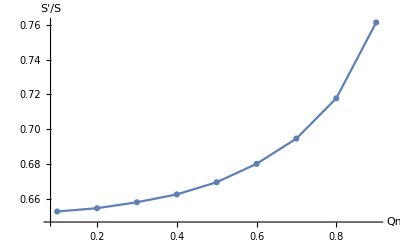

```mathematica
ListLinePlot[Table[{0.1m,shrink[[m]]},{m,1,9}],AxesLabel->{"Qm","S'/S"},PlotRange->All,PlotMarkers->Automatic]
```

```mathematica
σk=Table[√(1/(2π)NIntegrate[((shapedata[[m,2,10]][α]-shapedata[[m,1,10]][α])/(shapedata[[m,1,10]][α]))^2,{α,0,2π}]),{m,1,9}]
```

{0.199673,0.19864,0.196864,0.194679,0.191167,0.185995,0.178913,0.168385,0.147894}

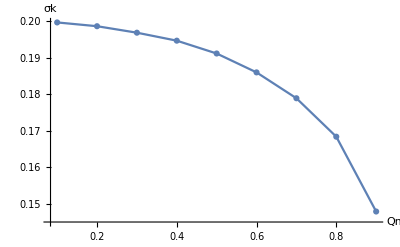

```mathematica
ListLinePlot[Table[{0.1m,σk[[m]]},{m,1,9}],AxesLabel->{"Qm","σk"},PlotRange->All,PlotMarkers->Automatic]
```